```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/santanu/Documents/disordered_triangular_swt/calc

# The Luttinger-Tisza Method for Anisotropic Lattice Anti-ferromagnet

## Energy function

```mathematica
EF[α_,β_,γ_,qx_,qy_]:=(1+α)Cos[qx]+(1+β)Cos[-qx/2+(√3 qy)/2]+(1+γ)Cos[-qx/2-(√3 qy)/2]
```

```mathematica
F[a_,b_]:=EF[α,β,γ,a,b]
```

```mathematica
S1[a_,b_]:=D[EF[α,β,γ,x,y],x]/.{x->a,y-> b}
```

```mathematica
S2[a_,b_]:=D[EF[α,β,γ,x,y],y]/.{x->a,y-> b}
```

```mathematica
Fxx[a_,b_]:=D[EF[α,β,γ,x,y],{x,2}]/.{x->a,y-> b}
```

```mathematica
Fxy[a_,b_]:=D[EF[α,β,γ,x,y],x,y]/.{x->a,y-> b}
```

```mathematica
Fyy[a_,b_]:=D[EF[α,β,γ,x,y],{y,2}]/.{x->a,y-> b}
```

### Energy minimization

```mathematica
SOLN1=Solve[S1[a,b]==0&&S2[a,b]==0,{a,b}];
```

```mathematica
SOLN2=FullSimplify[SOLN1/.{C[1]->0,C[2]->0},Assumptions-> {α∈Reals,β∈Reals,γ∈Reals,-1<α<1,-1<β<1,-1<γ<1}]
```

{{a→0,b→0},{a→0,b→-(2 π)/(√3)},{a→-π,b→π/(√3)},{a→-π,b→-π/(√3)},{a→π,b→π/(√3)},{a→π,b→-π/(√3)},{a→2 π,b→0},{a→2 π,b→-(2 π)/(√3)},{a→2 ArcTan[-√(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))],b→-1/(√3)2 ArcTan[(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(-β+γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]},{a→2 ArcTan[-(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))],b→-1/(√3)2 ArcTan[(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(β-γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]},{a→2 ArcTan[√((1+β) (1+γ) (1-α β+(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))],b→-1/(√3)2 ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(-β+γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]},{a→2 ArcTan[(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))],b→-1/(√3)2 ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(β-γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]}}

```mathematica
{a->2 ArcTan[-(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))],b->-1/(√3)2 ArcTan[(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(β-γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]}/.{α-> 0,β-> 0,γ-> 0}
```

{a→(4 π)/3,b→0}

```mathematica
FullSimplify[{a->2 ArcTan[-(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))],b->-1/(√3)2 ArcTan[(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(β-γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]}/.{α-> Subscript[J, 1]-1,β-> Subscript[J, 2]-1,γ-> Subscript[J, 3]-1},Assumptions-> {Subscript[J, 1]∈Reals,Subscript[J, 2]∈Reals,Subscript[J, 3]∈Reals}]
```

{a→2 ArcTan[-J_1 √(J_2 J_3 (-J_1^2 (J_2-J_3)^2+J_2^2 J_3^2)),J_1 √(J_2 J_3 (-J_2^2 J_3^2+J_1^2 (J_2+J_3)^2))],b→-(2 ArcTan[(J_2+J_3) √(J_2 J_3 (-J_1^2 (J_2-J_3)^2+J_2^2 J_3^2)),(J_2-J_3) √(J_2 J_3 (-J_2^2 J_3^2+J_1^2 (J_2+J_3)^2))])/(√3)}

```mathematica
FullSimplify[F[a,b]/.SOLN2,Assumptions-> {α∈Reals,β∈Reals,γ∈Reals,-1<α<1,-1<β<1,-1<γ<1}]
```

{3+α+β+γ,-1+α-β-γ,-1-α+β-γ,-1-α-β+γ,-1-α-β+γ,-1-α+β-γ,-1+α-β-γ,3+α+β+γ,-((1+β) (1+γ))/(1+α)+(1+α) Cos[2 ArcTan[-√(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 β+(2+β) γ+α (2+β+γ)))]],-((1+β) (1+γ))/(1+α)+(1+α) Cos[2 ArcTan[-(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 β+(2+β) γ+α (2+β+γ)))]],(1+β) Cos[ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(β-γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]-ArcTan[√((1+β) (1+γ) (1-α β+(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]+(1+α) Cos[2 ArcTan[√((1+β) (1+γ) (1-α β+(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]+(1+γ) Cos[ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(β-γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]+ArcTan[√((1+β) (1+γ) (1-α β+(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]],(1+α) Cos[2 ArcTan[(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 β+(2+β) γ+α (2+β+γ)))]]+(1+β) Cos[ArcTan[(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]-ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(-β+γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]+(1+γ) Cos[ArcTan[(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]+ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(-β+γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]}

```mathematica
FullSimplify[Fxx[a,b]/.SOLN2,Assumptions-> {α∈Reals,β∈Reals,γ∈Reals,-1<α<1,-1<β<1,-1<γ<1}]
```

{1/4 (-6-4 α-β-γ),1/4 (-2-4 α+β+γ),1/4 (4+4 α-β+γ),1/4 (4+4 α+β-γ),1/4 (4+4 α+β-γ),1/4 (4+4 α-β+γ),1/4 (-2-4 α+β+γ),1/4 (-6-4 α-β-γ),((1+β) (1+γ)+(2 (1+α (2+α) (2+β (2+β))+2 (α-β) (2+α+β) γ+(α-β) (2+α+β) γ^2))/((1+β) (1+γ)))/(4 (1+α)),((1+β) (1+γ)+(2 (1+α (2+α) (2+β (2+β))+2 (α-β) (2+α+β) γ+(α-β) (2+α+β) γ^2))/((1+β) (1+γ)))/(4 (1+α)),-1/4 (1+β) Cos[ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(β-γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]-ArcTan[√((1+β) (1+γ) (1-α β+(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]-(1+α) Cos[2 ArcTan[√((1+β) (1+γ) (1-α β+(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]-1/4 (1+γ) Cos[ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(β-γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]+ArcTan[√((1+β) (1+γ) (1-α β+(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]],-(1+α) Cos[2 ArcTan[(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 β+(2+β) γ+α (2+β+γ)))]]-1/4 (1+β) Cos[ArcTan[(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]-ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(-β+γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]-1/4 (1+γ) Cos[ArcTan[(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]+ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(-β+γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]}

```mathematica
FullSimplify[Fyy[a,b]/.SOLN2,Assumptions-> {α∈Reals,β∈Reals,γ∈Reals,-1<α<1,-1<β<1,-1<γ<1}]
```

{-3/4 (2+β+γ),3/4 (2+β+γ),-3/4 (β-γ),(3 (β-γ))/4,(3 (β-γ))/4,-3/4 (β-γ),3/4 (2+β+γ),-3/4 (2+β+γ),(3 (1+β) (1+γ))/(4 (1+α)),(3 (1+β) (1+γ))/(4 (1+α)),-3/4 (1+β) Cos[ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(β-γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]-ArcTan[√((1+β) (1+γ) (1-α β+(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]-3/4 (1+γ) Cos[ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(β-γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]+ArcTan[√((1+β) (1+γ) (1-α β+(2+α+β) γ) (1-α γ+β (2+α+γ))),-√((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]],-3/4 (1+β) Cos[ArcTan[(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]-ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(-β+γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]-3/4 (1+γ) Cos[ArcTan[(1+α) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(1+α) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]+ArcTan[-(2+β+γ) √(-(1+β) (1+γ) (-1+α β-(2+α+β) γ) (1-α γ+β (2+α+γ))),(-β+γ) √((1+β) (1+γ) (1-β γ+α (2+β+γ)) (3+2 γ+β (2+γ)+α (2+β+γ)))]]}

```mathematica
FullSimplify[Fxx[a,b]Fyy[a,b]-Fxy[a,b]^2/.SOLN2,Assumptions-> {α∈Reals,β∈Reals,γ∈Reals,-1<α<1,-1<β<1,-1<γ<1}]
```

$Aborted

### Expansion around infitesimal anisotropy

```mathematica
Collect[FullSimplify[Normal[Series[{a,b}/.SOLN2/.{α-> Z α,β-> Z β,γ->  Z γ},{Z,0,1}]]/.Z-> 1],{α,β,γ}]
```

{{0,0},{0,-(2 π)/(√3)},{-π,π/(√3)},{-π,-π/(√3)},{π,π/(√3)},{π,-π/(√3)},{2 π,0},{2 π,-(2 π)/(√3)},{-(4 π)/3+(2 α)/(√3)-β/(√3)-γ/(√3),β-γ},{(4 π)/3-(2 α)/(√3)+β/(√3)+γ/(√3),-β+γ},{-(2 π)/3-(2 α)/(√3)+β/(√3)+γ/(√3),-(2 π)/(√3)-β+γ},{(2 π)/3+(2 α)/(√3)-β/(√3)-γ/(√3),-(2 π)/(√3)+β-γ}}

```mathematica
Collect[FullSimplify[Normal[Series[F[a,b]/.SOLN2/.{α-> Z α,β-> Z β,γ->  Z γ},{Z,0,1}]]/.Z-> 1],{α,β,γ}]
```

{3+α+β+γ,-1+α-β-γ,-1-α+β-γ,-1-α-β+γ,-1-α-β+γ,-1-α+β-γ,-1+α-β-γ,3+α+β+γ,-3/2-α/2-β/2-γ/2,-3/2-α/2-β/2-γ/2,-3/2-α/2-β/2-γ/2,-3/2-α/2-β/2-γ/2}

```mathematica
FindMinimum[{EF[0.0,0.0,0.0,a,b],√(a^2+b^2)≤ 2π},{a,b}]
```

```mathematica
FindMinimum[{EF[1.0,0.0,0.0,a,b],√(a^2+b^2)≤ 2π},{a,b}]
```

```mathematica
FindMinimum[{EF[0.0,1.0,0.0,a,b],√(a^2+b^2)≤ 2π},{a,b}]
```

```mathematica
FindMinimum[{EF[0.0,3.0,0.0,a,b,],√(a^2+b^2)≤ 2π},{a,b}]
```

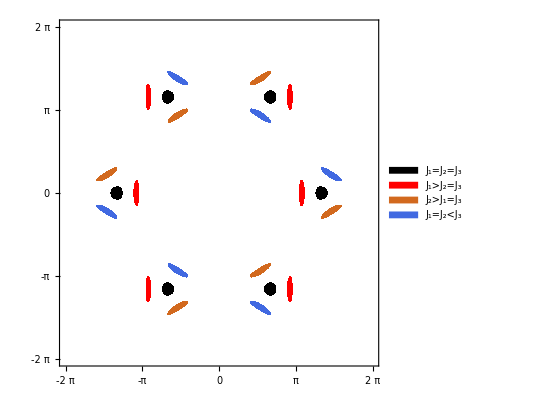

```mathematica
QS=RegionPlot[{EF[0.0,0.0,0.0,qx,qy]<-1.48,EF[3.0,0.0,0.0,qx,qy]<-4.105,EF[0.0,3.0,0.0,qx,qy]<-4.105,EF[0.0,0.0,3.0,qx,qy]<-4.105},{qx,-2π,2π},{qy,-2π,2π},BoundaryStyle->None,PlotPoints->100,PlotStyle-> {Black,RGBColor[1,0,0],RGBColor[0.823,0.411,0.117],RGBColor[0.254,0.411,0.882]},FrameTicks->{{-2π,-π,0,π,2π},{-2π,-π,0,π,2π}},PlotLegends-> Placed[SwatchLegend[{Style["J_1=J_2=J_3", FontSize-> 30],
Style["J_1>J_2=J_3",FontFamily-> "Helvetica", FontSize-> 30],Style["J_2>J_1=J_3",FontFamily-> "Helvetica", FontSize-> 30],Style["J_1=J_2<J_3",FontFamily-> "Helvetica", FontSize-> 30]},LabelStyle->30,LegendMarkers->"Bubble",LegendMarkerSize->20],Right],BaseStyle->{FontFamily->  "Helvetica", FontSize-> 25,Alignment->Center,FontColor->Black}]
```

```mathematica
Export["anisotropy-Q.pdf",QS,ImageSize->600,"AllowRasterization"-> False]
```

anisotropy-Q.pdf